# Graph convolutional regression of cardiac depolarization

## Phases 1-2: equation reference and deterministic synthetic evidence

## Scope and evidence

This notebook implements paper equations and a synthetic graph-wavefront demonstrator. It does not reproduce the unavailable trained 20-layer network or clinical experiments.

Loads the HeartGCNModel` package from src/HeartGCNModel.wl after fixing the RNG seed to 42 so every equation check and synthetic experiment is deterministic.

```mathematica
SeedRandom[42]; Get[FileNameJoin[{NotebookDirectory[], "src", "HeartGCNModel.wl"}]]
```

## Equation checks

MeanSAGEAggregate[neighbors] returns the componentwise mean of the neighbor feature vectors. If the neighborhood is empty, it returns a zero vector when an explicit Dimension option is given, otherwise Missing["EmptyNeighborhood"]. This is the mean GraphSAGE aggregate h_N(i) = mean(h_j, j in N(i)) (claim C1, Method pp. 2-3).

```mathematica
MeanSAGEAggregate[{{1, 2}, {3, 4}}]
```

{2,3}

GraphSAGEUpdate[self, neighborhood, parameters] applies the paper's vertex update h'_i = sigma(W_i h_i + b_i + W_N a_i + b_N), with weights shared over all vertices, then the activation (default leaky ReLU). This is claim C2 (Method, p. 3).

```mathematica
p = <|"SelfWeights" -> IdentityMatrix[2], "SelfBias" -> {0, 0}, "NeighborWeights" -> IdentityMatrix[2], "NeighborBias" -> {0, 0}, "Activation" -> Identity|>; GraphSAGEUpdate[{1, 2}, {{3, 4}, {5, 6}}, p]
```

{5,7}

WeightedLATMSE[prediction, truth, measuredMask] computes the LAT loss (1/N) Sum alpha_i (prediction_i - truth_i)^2 with alpha = 2 at measured vertices and 1 elsewhere (claim C3, p. 3). QRSDuration[times] = Max[times] - Min[times]. CombinedLoss returns <|LATLoss, QRSLoss, TotalLoss|> with TotalLoss = L_LAT + (QRS(prediction) - QRS(truth))^2 (claim C4, p. 3).

```mathematica
{WeightedLATMSE[{1, 2}, {0, 0}, {True, False}], CombinedLoss[{1, 3}, {1, 2}, {True, False}]}
```

{3,<|LATLoss→1/2,QRSLoss→1,TotalLoss→3/2|>}

AnisotropyTensor[f, r] builds the anisotropy matrix D = (1-r) f f^T + r IdentityMatrix with default r = 1/3; the fiber f is normalized and must be nonzero. VirtualEdgeLength[e, f, r] = Sqrt[e . D . e]. EdgeTravelTime[length, speed] = length / speed for positive speed and Infinity for zero speed, so scar edges are impassable (issue I7). These reproduce claim C5 (Data Generation, p. 5).

```mathematica
{AnisotropyTensor[{1, 0, 0}], VirtualEdgeLength[{2, 0, 0}, {1, 0, 0}], VirtualEdgeLength[{0, 3, 0}, {1, 0, 0}], EdgeTravelTime[6, 3]}
```

{{{1,0,0},{0,1/3,0},{0,0,1/3}},2,√3,2}

## Synthetic wavefront

SyntheticWavefront[spec] builds a deterministic rectangular unit-edge grid graph and computes ground-truth activation times as shortest-path distances from a single source. This demonstrates claim C6: activation follows shortest paths from activation points (Data Generation, p. 5). The grid is not cardiac anatomy and speed is uniform.

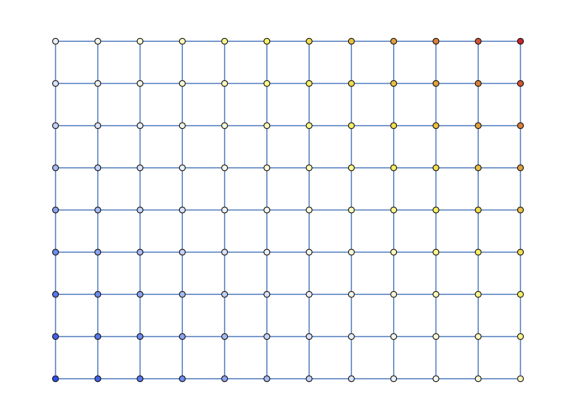

```mathematica
experiment = SyntheticWavefront[]; Graph[experiment["Graph"], VertexCoordinates -> experiment["Coordinates"], VertexStyle -> Thread[Range[Length[experiment["Truth"]]] -> (ColorData["TemperatureMap"] /@ Rescale[experiment["Truth"]])], ImageSize -> Large]
```

## Sparse reconstruction demonstrator

SparseReconstruction[experiment, fraction, noise] is a demonstrator, not the paper's trained GCN. It samples a fraction of vertices (SeedRandom[42]), adds optional Gaussian noise in synthetic LAT units, fixes the measured values, and solves the Kirchhoff Laplacian on the unknown vertices so the estimate is harmonic on the unobserved set. It returns <|Estimate, Truth, MeasuredIndices, MeasuredValues, MAE, Fraction, Noise, Method|>.

```mathematica
reconstruction = SparseReconstruction[experiment, .25, .25]; KeyTake[reconstruction, {"MAE", "Fraction", "Noise", "Method"}]
```

<|MAE→0.433089,Fraction→0.25,Noise→0.25,Method→Harmonic graph interpolation demonstrator; not trained HeartGCN|>

Interactive sweep over sampling fraction and noise showing how the demonstrator MAE changes. This is a qualitative sensitivity demonstration of claim C9 (error decreases as sampling increases), not a confidence interval.

```mathematica
Manipulate[Module[{r}, SeedRandom[42]; r = SparseReconstruction[experiment, fraction, noise]; ListDensityPlot[MapThread[Append, {experiment["Coordinates"], r["Estimate"]}], InterpolationOrder -> 0, PlotLabel -> Row[{"Demonstrator MAE: ", NumberForm[r["MAE"], 3]}]]], {fraction, .1, 1, .05}, {noise, 0, 1, .05}]
```

## Validation and key findings

RunValidationSuite[] runs 12 exact checks: mean aggregation, vertex update, weighted LAT MSE, QRS duration, combined zero loss, anisotropy eigenvalues, fiber and transverse virtual length, travel time, scar zero-speed blocked (Infinity), grid shortest-path propagation, and full-sample demonstrator recovery. It returns <|Seed, Tests, Passed, Failed, Total|>.

```mathematica
validation = RunValidationSuite[]; Print["KEY FINDINGS: ", validation["Passed"], "/", validation["Total"], " checks pass. Clinical MAE reproduction is unavailable."]; validation["Tests"]
```

KEY FINDINGS: 12/12 checks pass. Clinical MAE reproduction is unavailable.

{<|Name→mean aggregation exact,Passed→True|>,<|Name→vertex update exact,Passed→True|>,<|Name→weighted LAT MSE,Passed→True|>,<|Name→QRS duration,Passed→True|>,<|Name→combined zero loss,Passed→True|>,<|Name→anisotropy eigenvalues,Passed→True|>,<|Name→fiber virtual length,Passed→True|>,<|Name→transverse virtual length,Passed→True|>,<|Name→travel time,Passed→True|>,<|Name→scar zero speed blocked,Passed→True|>,<|Name→grid propagation,Passed→True|>,<|Name→full-sample demonstrator,Passed→True|>}

The package verifies aggregation, update, weighted LAT/QRS loss, anisotropic edge metric, travel time, and shortest-path propagation. Clinical reproduction is blocked by absent meshes, data, preprocessing constants, source code, and weights.